{25,25}

{25,25}

{25,25}

«2 more identical outputs»

{625,2,3}

{25,25,2,2}

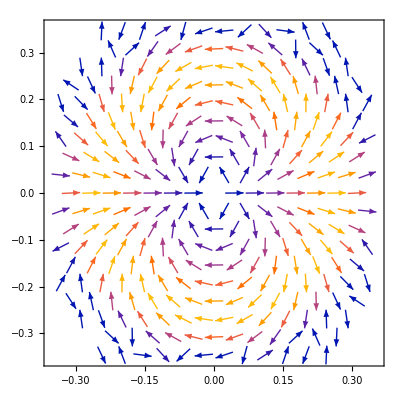

-Graphics3D-

```mathematica
(*导入数据*)s1=Import["G:\\坚果云\\我的坚果云\\2023SAM\\2_version斯格明子\\Fig.4_skyrmionsXY\\Fig.4(a)\\S1_Vis_z10.mat"];
s2=Import["G:\\坚果云\\我的坚果云\\2023SAM\\2_version斯格明子\\Fig.4_skyrmionsXY\\Fig.4(a)\\S2_Vis_z10.mat"];
s3=Import["G:\\坚果云\\我的坚果云\\2023SAM\\2_version斯格明子\\Fig.4_skyrmionsXY\\Fig.4(a)\\S3_Vis_z10.mat"];
x=Import["G:\\坚果云\\我的坚果云\\2023SAM\\2_version斯格明子\\Fig.4_skyrmionsXY\\Fig.4(a)\\x3.mat"];
y=Import["G:\\坚果云\\我的坚果云\\2023SAM\\2_version斯格明子\\Fig.4_skyrmionsXY\\Fig.4(a)\\y3.mat"];

(*提取实际数据，去除可能的嵌套*)
x=First[x];
y=First[y];
s1=First[s1];
s2=First[s2];
s3=First[s3];

(*检查维度*)
Print[Dimensions[x]];
Print[Dimensions[y]];
Print[Dimensions[s1]];
Print[Dimensions[s2]];
Print[Dimensions[s3]];

data=Flatten[Table[{{x[[i,j]],y[[i,j]],10},{s1[[i,j]],s2[[i,j]],s3[[i,j]]}},{i,1,Length[x]},{j,1,Length[x[[1]]]}],1];

data2D=Table[{{x[[i,j]],y[[i,j]]},{s1[[i,j]],s2[[i,j]]}},{i,1,Length[x]},{j,1,Length[x[[1]]]}];
Print[Dimensions[data]];
Print[Dimensions[data2D]];
ListVectorPlot[data2D]
ListVectorPlot3D[data,RegionFunction->Function[{x,y,z},9.9<z<10.01]]
```

```mathematica
ListDensityPlot[s2]
```

-Graphics-